```mathematica
SetDirectory[NotebookDirectory[]];
Needs["Strategies`",FileNameJoin[{Directory[],"Strategies.m"}]] (* Load Pegasus strategies package from current directory *)

(* Drawing primitive *)
DrawPlanarProb[prob_List, invariant_] := Module[{},
    { init, { f, {x, y}, H }, safe } = prob;
    {x1min, x1max} = {-6, 6};
    {x2min, x2max} = {-6, 6};
    
    Show[
      RegionPlot[Not[safe], {x, x1min, x1max}, {y, x2min, x2max}, PlotStyle -> Red, FrameLabel -> {x, y}, FrameTicks -> None, LabelStyle -> Directive[Large]], (* Plot unsafe states in red *)
      RegionPlot[init, {x, x1min, x1max}, {y, x2min, x2max}, PlotStyle -> Green], (* Plot initial states in green *)
      RegionPlot[Apply[And, invariant], {x, x1min, x1max}, {y, x2min, x2max}], (* Plot invariant *)
      StreamPlot[f, {x, x1min, x1max}, {y, x2min, x2max}, StreamStyle -> Darker[Gray]] (* Plot vector field *)
      ]
    ]
```

Get::noopen: Cannot open /home/s0805753/Work/KSP/KeYmaeraX/keymaerax-core/src/main/resources/pegasus-mathematicaClassifier.m.

Needs::nocont: Context Classifier` was not created when Needs was evaluated.

Get::noopen: Cannot open /home/s0805753/Work/KSP/KeYmaeraX/keymaerax-core/src/main/resources/pegasus-mathematicaQualitativeMethods.m.

Needs::nocont: Context QualitativeMethods` was not created when Needs was evaluated.

Get::noopen: Cannot open /home/s0805753/Work/KSP/KeYmaeraX/keymaerax-core/src/main/resources/pegasus-mathematicaAbstractionPolynomials.m.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Needs::nocont: Context AbstractionPolynomials` was not created when Needs was evaluated.

General::stop: Further output of Needs::nocont will be suppressed during this calculation.

### One-dimensional system tests

```mathematica
Directory[]
```

/home/s0805753

```mathematica
(* One-dimensional systems *)
```

### Constant right-hand side system tests

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

CONSTANT STRATEGY

4 x+x^2-4 y+y^2≤-23/3||(x+2 y≥2&&24 x+4 x^2-12 y-4 x y+y^2≤-103/3)||(x+2 y≥2&&-16 x+4 x^2+8 y-4 x y+y^2≤-11)||(x>0&&-4 x+x^2+y^2≤-3)

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{(x+2 y≥2&&(103+3 (4 x (6+x)-4 x y+y^2)≤36 y||11+4 x^2+y (8+y)≤4 x (4+y)))||3+x^2+y^2≤4 x||23+3 x (4+x)+3 (-4+y) y≤0},True}

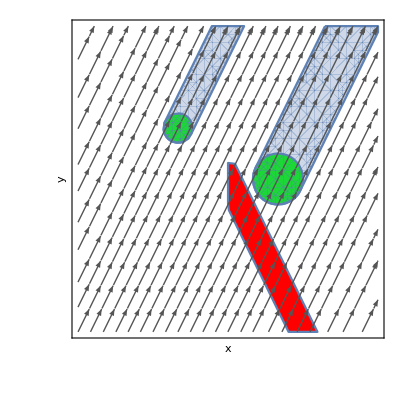

```mathematica
constantRhs1={
(x-2)^2+y^2≤1 || (x+2)^2+(y-2)^2≤1/3, 
{{1, 2},{x,y}, True},
  (-1/2y-x)^2≥1/3 ||x<=0
};
constantRhsInv1=Pegasus[constantRhs1]
DrawPlanarProb[constantRhs1, constantRhsInv1//First]
```

### Two-dimensional linear system tests

```mathematica
planarLin1={
x≤1 && x==0 && y==1,
{{x'=y,y'=-x},{x,y}, True},
x≤1
};
 planarLinInv1=Pegasus[planarLin1]
DrawPlanarProb[planarLin1, planarLinInv1//First];
```

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

GENERAL LINEAR STRATEGY

Trying first integrals first

{0,1-x^2-y^2}

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{True,x^2+y^2==1},True}

Precondition implies postcondition. Proceeding.

Postcondition is not an invariant. Proceeding.

Precondition is not an invariant. Proceeding.

GENERAL LINEAR STRATEGY

Trying first integrals first

{-87/5-3 x y,-38/5-3 x y,-11/4-3 x y,11/4-3 x y,53/22-x^2-4 y^2,6-x^2-4 y^2,82/7-x^2-4 y^2,185/6-x^2-4 y^2}

Relaxed invariant is still ok. Proceeding

Generated invariant implies postcondition. Returning.

{{x^2+4 y^2≥53/22,x^2+4 y^2≤185/6},True}

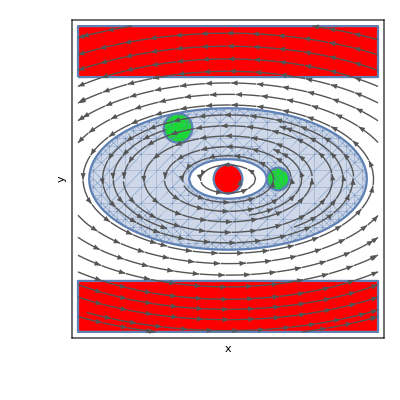

```mathematica
planarLin2={
(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3, 
{{-4y, x},{x,y}, True}, 
 y≤4 &&y≥-4 &&Not[x^2+y^2≤1/3]
};
planarLinInv2=Pegasus[planarLin2]
DrawPlanarProb[planarLin2, planarLinInv2//First]
```

```mathematica
planarLin3={
(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3,
 {{2x-y, -3*x+y},{x,y}, True},  
(x-1)^2+(y+5)^2≥2
};
planarLinInv3=Pegasus[planarLin3]
DrawPlanarProb[planarLin3, planarLinInv3//First]
```

```mathematica
planarLin4={
(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3, 
{{-2x+y, x-3*y},{x,y}, True}, 
 Not[(y≥1)&&(x≤1 && x≥0) || x^2+(y+3)^2≤1 || (x+6)^2+(y-1)^2≤1/3]
};
planarLinInv4=Pegasus[planarLin4]
DrawPlanarProb[planarLin4, planarLinInv4//First]
```

#### Higher-dimensional linear system tests

#### Planar non-linear system tests

```mathematica
planarNonLin1={
x>-4/5&&x<-1/3&&y<3/2&&y≥1, 
{{-x+a*x(x^2+y^2),x+a*y(x^2+y^2)}/.{a->1},{x,y}, True},
x≥-1/3||y<0||2 y≥1||x≤-4/5
};


 planarNonLinInv1=Pegasus[planarNonLin1]
DrawPlanarProb[planarNonLin1, planarNonLinInv1//First]
```

```mathematica
planarNonLin2={
(x-1)^2+y^2<1/4, 
{{(-1+x^2) (-(-2+√5)^2+x^2) (x+√5*y),(√5 x+y) (-1+y^2) (-(-2+√5)^2+y^2)},{x,y}, True},
 y<1 && x>-3
};
planarNonLinInv2=Pegasus[planarNonLin2]
DrawPlanarProb[planarNonLin2,  planarNonLinInv2//First]
```

#### Higher-dimensional non-linear system tests

```mathematica
Linear`FirstIntegralMethod[(x-2)^2+y^2≤1/5 || (x+2)^2+(y-2)^2≤1/3,Not[(y≥1)&&(x≤1 && x≥0) || x^2+(y+3)^2≤1 || (x+6)^2+(y-1)^2≤1/3],
 {{-2x+y, x-3*y},{x,y}, True}, RationalsOnly->True, RationalPrecision->3]
```

```mathematica
FirstIntegralGen`FindFirstIntegrals[2, {x,y}, {-2x+y, x-3*y}]
```